Author: Stephen C. Wein, Quantum Information Research Scientist at Quandela
Email:  stephen.wein@quandela.com
Date:   September 20th, 2023

## Exact scattering probabilities for a square pulse

This notebook computes the exact scattering probabilities for a two-level emitter driven by a square pulse in the semi-classical approximation. The approach uses perturbation theory and analytic recursive time integration. The solution is used to benchmark the numerical ZPG method presented in the paper “Exponential speedup for simulating photon counting from dynamic quantum sources” available online at:
 https://arxiv.org/abs/2307.16591

Note: it should take 20-30 minutes to evaluate the expressions for up to 6 photons using this notebook. The result is copied into the notebook for your convenience.

### Functions to build master equations

```mathematica
(*
Author: Stephen C.Wein,Quantum Information Research Scientist at Quandela
Email: stephen.wein@quandela.com
Date: September 20th,2023
*)

(* Finite system operator *)
Clear[Lower];
Lower::usage="Lower[i, j, N]
Inputs are three positive integers i, j, and N.
Output is a lowering operator from state j to state i where N is the total number of states.
";
Lower[i_Integer,j_Integer,Nmax_Integer]/;0<i≤Nmax&&0<j≤Nmax:=KroneckerProduct[UnitVector[Nmax,i],UnitVector[Nmax,j]];
Lower[i_Integer,j_Integer]/;0<i&&0<j:=Lower[i,j,Max[i,j,2]];
Lower[i_Integer]/;0<i:=Lower[i,i,Max[i,2]];
Lower[]:=Lower[1,2,2];

(*  Computes matrix representation of J(A,B) defined J(A,B)ρ = AρB^+ *)
Clear[SuperJ];
SuperJ::usage="SuperJ[A]
Input is an operator A.
Output is the linear 'jump' superoperator J(A)ρ = A.ρ.A†
	in its matrix representation SuperJ[A]=A ⊗ A^*.
";
SuperJ[A_?SquareMatrixQ,B_?SquareMatrixQ]/;SameQ@@Dimensions/@{A,B}:=KroneckerProduct[A,B*];
SuperJ[A:_?SquareMatrixQ:Lower[]]:=SuperJ[A,A];(* Jump *)


(* Left-acting superoperator defined S(A)ρ = Aρ *)
Clear[SuperL];
SuperL::usage="SuperL[A]
Input is an operator A.
Output is the linear superoperator applying A to the left L(A)ρ = A.ρ
	in its matrix representation SuperL[A]=A ⊗ I.
";
SuperL[A:_?SquareMatrixQ:Lower[]]:=KroneckerProduct[A,IdentityMatrix[Dimensions[A]]];


(* Right-acting superoperator defined R(A)ρ = ρA *)
Clear[SuperR];
SuperR::usage="SuperR[A]
Input is an operator A.
Output is the linear superoperator applying A to the right R(A)ρ = ρ.A
	in its matrix representation SuperR[A]=I ⊗ A^T.
";
SuperR[A:_?SquareMatrixQ:Lower[]†]:=KroneckerProduct[IdentityMatrix[Dimensions[A]],Transpose[A]];


(*  Computes matrix representation of D(A,B) defined D(A,B)ρ = AρB^+ - (B^+Aρ+ρB^+A)/2 *)
Clear[SuperD];
SuperD::usage="SuperD[A]
Input is an operator A.
Output is the linear Lindblad dissipator superoperator D(A)=J(A) - (L(A) + R(A))/2
	defined by D(A)ρ = A.ρ.A† - (A†.A.ρ + ρ.A†.A)/2
	in its matrix representation SuperD[A]=A ⊗ A^* - (A†.A ⊗ I + I ⊗ A^T.A^*)/2.
";
SuperD[A_?SquareMatrixQ,B_?SquareMatrixQ]/;SameQ@@Dimensions/@{A,B}:=SuperJ[A,B]-(SuperL[B†.A]+SuperR[B†.A])/2;
SuperD[A_?SquareMatrixQ]:=SuperD[A,A];(* Dissipation *)


(*  Computes matrix representation of C(A) defined C(A)ρ = [A,ρ] *)
Clear[SuperC];
SuperC::usage="SuperC[A]
Input is an operator A.
Output is the linear Lindblad commutation superoperator C(A)=L(A) - R(A)
	defined by C(A)ρ = [A,ρ]
	in its matrix representation SuperC[A]=A ⊗ I - I ⊗ A^T.
";
SuperC[A_?SquareMatrixQ]:=SuperL[A]-SuperR[A];(* Commutation *)

(* Trace vector in the Fock-Liouville space *)
Clear[TrVec];
TrVec::usage="TrVec[N]
Input is a positive integer N.
Output is a the N^2-dimensional identity vector |I_N⟩⟩ = ⟨⟨I_N| in the Fock-Liouville space.
";
TrVec[N_]/;NumberQ[N]&&N>0:=Flatten[IdentityMatrix[N]];
```

### Square pulse scattering

```mathematica
$Assumptions={Θ>0,τ>0};

σ=Lower[];(* Lowering (dipole) operator *)
H=(Θ/τ)(σ+σ†)/2;(* Hamiltonian *)
J=SuperJ[σ];(* Detector jump operator *)

(* Zero-photon conditional propagator *)
Clear[prop];
prop[t_,t0_]:=MatrixExp[(t-t0)(-ⅈ*SuperC[H]+SuperD[σ]-J)];

(* nth-order conditional state, recursive integration *)
Clear[cstate];
cstate[n_]:=cstate[n]=Integrate[prop[tf,t].J.(cstate[n-1]/.tf->t),{t,0,tf},PrincipalValue->True]//Simplify;
cstate[0]:=prop[tf,0].{1,0,0,0};(* Zero-photon conditional state *)
cstate[-1]=0cstate[0];

(* Conditional propagators after pulse ends (can emit at most 1 photon) *)
pinf[0]=SuperJ[σ.σ†];(* 0-photon decay *)
pinf[1]=SuperJ[σ];(* 1-photon decay *)
```

```mathematica
(* Combine piecewise time-independent solutions (excite + decay), this cell takes 20-30 minutes to evaluate! *)
pdistribution=Table[TrVec[2].(pinf[0].cstate[n]+pinf[1].cstate[n-1])/.tf->τ,{n,0,6}];
```

```mathematica
(* The full solution is presented here for simplicity *)
pdistributionStored={(2 ⅇ^(-τ/2) Θ^2)/(4 Θ^2-τ^2)-(ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) (-2 Θ^2+τ^2-τ √(-4 Θ^2+τ^2)))/(2 (4 Θ^2-τ^2))-(ⅇ^(1/2 (-τ+√(-4 Θ^2+τ^2))) (-2 Θ^2+τ^2+τ √(-4 Θ^2+τ^2)))/(2 (4 Θ^2-τ^2)),-(ⅇ^(-τ/2) (-2+ⅇ^(τ/2+1/2 (-τ-√(-4 Θ^2+τ^2)))+ⅇ^(τ/2+1/2 (-τ+√(-4 Θ^2+τ^2)))) Θ^2)/(4 Θ^2-τ^2)+(ⅇ^(-τ/2) Θ^2 (4 (Θ^2 τ+τ^2)+(-2 Θ^2 τ+(-4+τ) τ^2) Cosh[1/2 √(-4 Θ^2+τ^2)]+(τ ((-2+τ) τ^2-4 Θ^2 (1+τ)) Sinh[1/2 √(-4 Θ^2+τ^2)])/(√(-4 Θ^2+τ^2))))/((-4 Θ^2+τ^2)^2),1/(4 (-4 Θ^2+τ^2)^4)ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^4 (4 Θ^2 τ^2 (2 (7+16 ⅇ^(1/2 √(-4 Θ^2+τ^2))+7 ⅇ^(√(-4 Θ^2+τ^2))) τ+(-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))-2 τ^4 ((7+16 ⅇ^(1/2 √(-4 Θ^2+τ^2))+7 ⅇ^(√(-4 Θ^2+τ^2))) τ+5 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+4 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ^2 (16 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) Θ^2+τ (8 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ+15 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+τ^2 (4 Θ^2-τ^2) (2 (1+8 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2-τ ((1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))))+(2 ⅇ^(-τ/2) Θ^4 (2 τ+τ Cosh[1/2 √(-4 Θ^2+τ^2)]-(6 τ Sinh[1/2 √(-4 Θ^2+τ^2)])/(√(-4 Θ^2+τ^2))))/((-4 Θ^2+τ^2)^2),(ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^6 (96 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2)))^2 τ^2-18 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^2 √(-4 Θ^2+τ^2)+(1-8 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) τ^2 (-4 Θ^2+τ^2)))/(2 (-4 Θ^2+τ^2)^4)+1/(12 (-4 Θ^2+τ^2)^(11/2))ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^6 (-24 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ^3 (70 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) Θ^2+τ (35 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ+64 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+τ^3 (4 Θ^2-τ^2) (-τ^2 ((-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+2 Θ^2 (2 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(1-16 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-6 τ^3 (-4 Θ^2+τ^2) (-4 (-1+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ (4 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(5-16 ⅇ^(1/2 √(-4 Θ^2+τ^2))+5 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+12 τ^3 (2 Θ^2 (-58 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(3+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+3 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 (29 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(19+32 ⅇ^(1/2 √(-4 Θ^2+τ^2))+19 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))),1/(48 (-4 Θ^2+τ^2)^7)ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^8 (240 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ^4 (256 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) Θ^2+τ (128 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ+231 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-τ^4 (-4 Θ^2+τ^2)^2 (2 (1+32 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2-τ ((1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-4 τ^4 (-4 Θ^2+τ^2) (-2 Θ^2 (2 (13+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+13 ⅇ^(√(-4 Θ^2+τ^2))) τ+7 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 ((13+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+13 ⅇ^(√(-4 Θ^2+τ^2))) τ+11 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-120 τ^4 (2 Θ^2 (-2 (103+256 ⅇ^(1/2 √(-4 Θ^2+τ^2))+103 ⅇ^(√(-4 Θ^2+τ^2))) τ+23 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 ((103+256 ⅇ^(1/2 √(-4 Θ^2+τ^2))+103 ⅇ^(√(-4 Θ^2+τ^2))) τ+65 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+12 τ^4 (-4 Θ^2+τ^2) (-2 (13+384 ⅇ^(1/2 √(-4 Θ^2+τ^2))+13 ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ ((69-128 ⅇ^(1/2 √(-4 Θ^2+τ^2))+69 ⅇ^(√(-4 Θ^2+τ^2))) τ+95 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))))-(ⅇ^(-τ/2) Θ^8 (-32 Θ^2 τ^3+8 τ^3 (96+τ^2)+(-4 Θ^2 τ^3+τ^3 (492+τ^2)) Cosh[1/2 √(-4 Θ^2+τ^2)]-(36 τ (-4 Θ^2 τ^2+τ^2 (70+τ^2)) Sinh[1/2 √(-4 Θ^2+τ^2)])/(√(-4 Θ^2+τ^2))))/(3 (4 Θ^2-τ^2) (-4 Θ^2+τ^2)^4),1/(24 (-4 Θ^2+τ^2)^7)ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^10 (92160 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2)))^2 τ^4-18360 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^4 √(-4 Θ^2+τ^2)+60 (25-128 ⅇ^(1/2 √(-4 Θ^2+τ^2))+25 ⅇ^(√(-4 Θ^2+τ^2))) τ^4 (-4 Θ^2+τ^2)-60 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^4 (-4 Θ^2+τ^2)^(3/2)+(1-32 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) τ^4 (-4 Θ^2+τ^2)^2)-1/(240 (-4 Θ^2+τ^2)^(17/2))ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^10 (10080 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ^5 (286 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) Θ^2+τ (143 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ+256 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+τ^5 (-4 Θ^2+τ^2)^2 (-τ^2 ((-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+2 Θ^2 (2 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(1-64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+10 τ^5 (-4 Θ^2+τ^2)^2 (-10 (-1+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ (7 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+8 (1-8 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-20 τ^5 (-4 Θ^2+τ^2) (Θ^2 (-564 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ-2 (41-1024 ⅇ^(1/2 √(-4 Θ^2+τ^2))+41 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 (141 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(109+256 ⅇ^(1/2 √(-4 Θ^2+τ^2))+109 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+360 τ^5 (-4 Θ^2+τ^2) (4 (-1+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ (104 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(151-512 ⅇ^(1/2 √(-4 Θ^2+τ^2))+151 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-720 τ^5 (Θ^2 (-3164 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+2 (233+1536 ⅇ^(1/2 √(-4 Θ^2+τ^2))+233 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 (791 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(489+1024 ⅇ^(1/2 √(-4 Θ^2+τ^2))+489 ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))),1/(120 (-4 Θ^2+τ^2)^(17/2))ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^12 (-4324320 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^5+5040 (173+512 ⅇ^(1/2 √(-4 Θ^2+τ^2))+173 ⅇ^(√(-4 Θ^2+τ^2))) τ^5 √(-4 Θ^2+τ^2)-75600 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^5 (-4 Θ^2+τ^2)+60 (59+512 ⅇ^(1/2 √(-4 Θ^2+τ^2))+59 ⅇ^(√(-4 Θ^2+τ^2))) τ^5 (-4 Θ^2+τ^2)^(3/2)-90 (-1+ⅇ^(√(-4 Θ^2+τ^2))) τ^5 (-4 Θ^2+τ^2)^2+(1+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) τ^5 (-4 Θ^2+τ^2)^(5/2))+1/(1440 (-4 Θ^2+τ^2)^10)ⅇ^(1/2 (-τ-√(-4 Θ^2+τ^2))) Θ^12 (20160 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ^6 (8192 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) Θ^2+τ (4096 (-1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) τ+7293 (1+ⅇ^(1/2 √(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+τ^6 (4 Θ^2-τ^2)^3 (2 (1+128 ⅇ^(1/2 √(-4 Θ^2+τ^2))+ⅇ^(√(-4 Θ^2+τ^2))) Θ^2-τ ((1+ⅇ^(√(-4 Θ^2+τ^2))) τ+(-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-6 τ^6 (-4 Θ^2+τ^2)^2 (-2 Θ^2 ((38+512 ⅇ^(1/2 √(-4 Θ^2+τ^2))+38 ⅇ^(√(-4 Θ^2+τ^2))) τ+13 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 ((19+256 ⅇ^(1/2 √(-4 Θ^2+τ^2))+19 ⅇ^(√(-4 Θ^2+τ^2))) τ+17 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-6720 τ^6 (-4 Θ^2+τ^2) (-Θ^2 (8 (13+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+13 ⅇ^(√(-4 Θ^2+τ^2))) τ+7 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 (2 (13+64 ⅇ^(1/2 √(-4 Θ^2+τ^2))+13 ⅇ^(√(-4 Θ^2+τ^2))) τ+19 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+60 τ^4 (-4 Θ^2 τ+τ^3)^2 (-2 (39+1280 ⅇ^(1/2 √(-4 Θ^2+τ^2))+39 ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ ((79-256 ⅇ^(1/2 √(-4 Θ^2+τ^2))+79 ⅇ^(√(-4 Θ^2+τ^2))) τ+98 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))+5040 τ^6 (-4 Θ^2+τ^2) (2 (69-2048 ⅇ^(1/2 √(-4 Θ^2+τ^2))+69 ⅇ^(√(-4 Θ^2+τ^2))) Θ^2+τ ((415-1024 ⅇ^(1/2 √(-4 Θ^2+τ^2))+415 ⅇ^(√(-4 Θ^2+τ^2))) τ+623 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2)))-10080 τ^6 (2 Θ^2 (-2 (3197+8192 ⅇ^(1/2 √(-4 Θ^2+τ^2))+3197 ⅇ^(√(-4 Θ^2+τ^2))) τ+1093 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))+τ^2 ((3197+8192 ⅇ^(1/2 √(-4 Θ^2+τ^2))+3197 ⅇ^(√(-4 Θ^2+τ^2))) τ+1951 (-1+ⅇ^(√(-4 Θ^2+τ^2))) √(-4 Θ^2+τ^2))))};
```

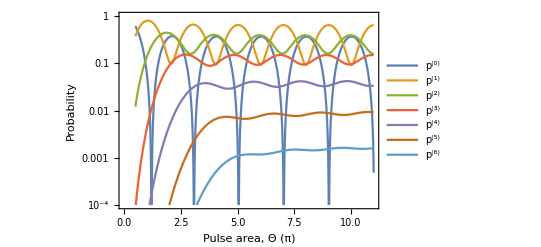

```mathematica
LogPlot[pdistributionStored/.{τ->2,Θ->x*π}//Re//Evaluate,{x,0.5,11},PlotRange->{10^-4,1},Frame->True,BaseStyle->13,FrameStyle->Black,FrameLabel->{"Pulse area, Θ (π)","Probability"},PlotLegends->Placed[Superscript["p","("<>ToString[#]<>")"]&/@Range[0,6],Right]]
```

```mathematica
pdistributionStored/.{τ->2,Θ->10π}//N//Re
```

{0.36767,0.0925185,0.39255,0.0956782,0.0414044,0.00832104,0.00159106}

```mathematica
{0.3676696534878473,0.09251845596353653,0.3925503724545842,0.09567822259508903,0.04140436181229831,0.008321043393002223,0.0015910611400041256}
```